# A Simple Example

Gary S. Anderson

## Luca’s Simplest Financial Market Model

### Model and Initial Polynomial Basis Definition

#### Provide Model Equations and Generate an instance of the Model’s Class ( a Subclass of DoEqns )

```mathematica
lucaEqns={qq[t]-(betap*(1-rhop)*qq[t+1]+rhop*qq[t-1]-sigmap*rr[t]+ru[t]),rr[t]-phip*qq[t],ru[t]-rho$ru*ru[t-1]-adj*eps[uu][t]};
newWeightedStochasticBasis[lucaMod,lucaEqns];
{{stateVar,nonStateVar,theShock},modEqns}=GenerateModelCode[lucaMod];
```

"c:\Program Files\Java\jdk1.7.0_51\bin\javac" -cp ./;ProjectionMethodToolsJava-0.0.1-SNAPSHOT.jar;Jama-1.0.2-1.0-SNAPSHOT.jar  -target 1.7 ./lucaMod.java

A list of equations constitutes the model’s definition. The state and non-state variables are of the form symbolName[t-1|t|t+1]. The shocks are of the form eps[symbolName][t].  The shocks and the variables with time index t-1 constitute the state variables. The newWeigthedStochasticBasis function associates features of the model definition with Mathematica upvalues of a variable.

#### Provide the Model Instance With Values for its Parameters

```mathematica
lucaSubs={betap->99/100,phip->1,rhop->1/2,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{5},sigma$u->0.02,theMean->{0},rho$ru-> 0.5,adj->0.0000000001};
modParams={adj,betap,phip,rhop, rho$ru,sigmap}//.lucaSubs//N;
modEqns[updateParams[modParams]]
```

#### Provide Parameters for the Initial Polynomial Basis and Generate an Instance of the WeightedStochasticBasis Class

```mathematica
polyRange={{ruLow,ruHigh},{qLow,qHigh}}/.lucaSubs;
initPower={1,1};shockPower={1};
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

### Symbolic Computation for First Degree

The mathematica program simpleFin.mth computes these values.

```mathematica
hmat={{-rhop,0,0,1,sigmap,-1,-(betap*(1-rhop)),0,0},{0,0,0,-phip,1,0,0,0,0},{0,0,-rho$ru,0,0,1,0,0,0}};
bmat={{(2*rhop)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),0,(2*rho$ru)/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{(2*phip*rhop)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),0,(2*phip*rho$ru)/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{0,0,rho$ru}};
phimat={{2/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),(-2*sigmap)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),2/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{(2*phip)/(1+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]),(2*betap*(-1+rhop)*rhop+phip*sigmap*(1+phip*sigmap-Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]))/(2*betap*(-1+rhop)*rhop),(2*phip)/(1+2*betap*(-1+rhop)*rho$ru+phip*sigmap+Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])},{0,0,1}};
fmat={{(1+phip*sigmap-Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2])/(2*rhop),0,0},{(phip*(1+phip*sigmap-Sqrt[4*betap*(-1+rhop)*rhop+(1+phip*sigmap)^2]))/(2*rhop),0,0},{0,0,0}};
```

```mathematica
{bmat,phimat,fmat}//.lucaSubs//N;
```

```mathematica
psimat={{0},{0},{1}};
```

```mathematica
Thread[{{qq[t]},{rr[t]},{ru[t]}}== (bmat .{{qq[t-1]},{rr[t-1]},{ru[t-1]}}) + phimat . psimat.{{eps[uu][t]}}]//.lucaSubs//N
```

{{qq[t]}=={0.267742 qq[-1.+t]+0.308648 ru[-1.+t]+0.617296 eps[uu][t]},{rr[t]}=={0.267742 qq[-1.+t]+0.308648 ru[-1.+t]+0.617296 eps[uu][t]},{ru[t]}=={0.5 ru[-1.+t]+eps[uu][t]}}

```mathematica
bmat//.lucaSubs//N
```

{{0.267742,0.,0.308648},{0.267742,0.,0.308648},{0.,0.,0.5}}

```mathematica
someVars={JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.GridVarSpec","xx",0,2],
JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.GridVarSpec","yy",-5,7],
JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.GridVarSpec","zz",1,70]};
 tgv=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.GridVars",someVars];
 theOrds123={1,1,1};
 theGS111=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.GridPointsSpec",tgv,theOrds123];
```

```mathematica
InstallJava[]
```

LinkObject[…]

```mathematica
matOrd=theGS111[generatePolyOrdersForOuterProduct[]]
```

{{0,0,0},{1,0,0},{0,1,0},{1,1,0},{0,0,1},{1,0,1},{0,1,1},{1,1,1}}

```mathematica
tryMat=ReplacePart[ConstantArray[0,{3,8}],{{1,2}->bmat[[1,1]],{1,3}->bmat[[1,3]],{1,5}->phimat[[1,3]],{2,2}->bmat[[2,1]],{2,3}->bmat[[2,3]],{2,5}->phimat[[2,3]],{3,2}->bmat[[3,1]],{3,3}->bmat[[3,3]],{3,5}->phimat[[3,3]]}]//.lucaSubs//N
```

{{0.,0.267742,0.308648,0.,0.617296,0.,0.,0.},{0.,0.267742,0.308648,0.,0.617296,0.,0.,0.},{0.,0.,0.5,0.,1.,0.,0.,0.}}

### Collocation Solution Computations

#### Compute Initial Solution, Check for Convergence and Display the Polynomial Approximation

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)(*tryMat=ArrayFlatten[{{ConstantArray[0,{3,9}],{{0.000000000000001,0.292289373557350,0.000000000000001,0.000000000000000,0.000000278748869,0.000000000000000,0.000000000000000,0.000000000000001,0.000000000000000},{0,0,0,0,rho$ru,0,0,0,0},{0,0,0,0,rho$ru,0,0,0,0}}}}]//.lucaSubs;*)
(*tryMat=ConstantArray[0,{3,8}];tryMat=ReplacePart[tryMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
lucaBasis[setAllWeights[tryMat]]

simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$1=ComputeInitialCollocationWeights[lucaBasis,tryMat,modEqns,simp];If[res1$1$1[isConvergedQ[]],
polys1$1$1=genPolys[res1$1$1[getResWeights[]],Join[stateVar,theShock],lucaBasis[getRanges[]],res1$1$1[getOrders[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]
```

{0.308648 ru+0.749724 uu$Shock,0.5 ru,0.308648 ru+0.749724 uu$Shock}

```mathematica
huh=getAllFVals[res1$1$1];
```

```mathematica
huh[[1]]//Dimensions
```

{10,24,1}

```mathematica
TableForm[huh[[1]]]
```

0.0470165 | 0.589495 | -0.165154 | 0.377324 | -0.377324 | 0.165154 | -0.589495 | -0.0470165 | 0.216596 | 0.595241 | -0.0540162 | 0.324629 | -0.324629 | 0.0540162 | -0.595241 | -0.216596 | 0.667287 | 0.288643 | 0.584346 | 0.205702 | -0.205702 | -0.584346 | -0.288643 | -0.667287
-220.994 | -118.894 | -109.337 | -7.23677 | 17.6996 | 119.8 | 129.356 | 231.457 | -1.77636×10^-15 | 8.88178×10^-16 | -8.88178×10^-16 | 3.33067×10^-15 | -2.44249×10^-15 | 1.77636×10^-15 | -3.55271×10^-15 | -1.77636×10^-15 | -1.87398×10^-15 | 1.95629×10^-15 | -2.34582×10^-15 | 1.92854×10^-15 | 4.30688×10^-16 | 2.37358×10^-15 | 6.24977×10^-16 | 1.01355×10^-15
-56.6538 | -31.2143 | -28.7328 | -3.29332 | 2.76158 | 28.201 | 30.6826 | 56.122 | 1.77636×10^-15 | -1.77636×10^-15 | -2.22045×10^-15 | -1.66533×10^-15 | 1.92598×10^-15 | 2.66454×10^-15 | -2.22045×10^-15 | 4.44089×10^-15 | 1.34015×10^-17 | -1.43541×10^-17 | 4.1157×10^-17 | 1.34015×10^-17 | -1.34015×10^-17 | -4.1157×10^-17 | 1.43541×10^-17 | -1.34015×10^-17
-14.8525 | -8.57753 | -7.87554 | -1.60053 | -0.246957 | 6.02806 | 6.73005 | 13.0051 | -1.33227×10^-15 | -8.88178×10^-16 | -2.22045×10^-16 | 8.88178×10^-16 | -1.33227×10^-15 | 4.44089×10^-16 | -3.77476×10^-15 | -3.10862×10^-15 | -1.43541×10^-17 | 1.34015×10^-17 | -4.21097×10^-17 | -1.43541×10^-17 | 1.43541×10^-17 | 4.21097×10^-17 | -1.34015×10^-17 | 1.43541×10^-17
-4.0208 | -2.53357 | -2.297 | -0.809771 | -0.596268 | 0.890958 | 1.12754 | 2.61476 | -2.22045×10^-16 | 0. | 3.33067×10^-16 | 4.44089×10^-16 | 4.996×10^-16 | -2.22045×10^-16 | 1.58207×10^-15 | 1.11022×10^-16 | 1.34015×10^-17 | -1.43541×10^-17 | 4.1157×10^-17 | 1.34015×10^-17 | -1.34015×10^-17 | -4.1157×10^-17 | 1.43541×10^-17 | -1.34015×10^-17
-1.08705 | -0.785082 | -0.697659 | -0.395695 | -0.410835 | -0.10887 | -0.0214482 | 0.280517 | -2.22045×10^-16 | 1.11022×10^-16 | -1.11022×10^-16 | -2.77556×10^-16 | 4.71845×10^-16 | 4.30211×10^-16 | 2.77556×10^-17 | 1.38778×10^-17 | -1.43541×10^-17 | 1.34015×10^-17 | -4.21097×10^-17 | -1.43541×10^-17 | 1.43541×10^-17 | 4.21097×10^-17 | -1.34015×10^-17 | 1.43541×10^-17
-0.22942 | -0.19413 | -0.174421 | -0.13913 | -0.154475 | -0.119184 | -0.0994753 | -0.064185 | -5.20417×10^-17 | -2.498×10^-16 | -1.11022×10^-16 | -2.77556×10^-16 | -2.15106×10^-16 | 1.04083×10^-16 | -2.22045×10^-16 | -4.996×10^-16 | 1.79935×10^-16 | -6.98653×10^-17 | 4.1157×10^-17 | 1.24424×10^-16 | 2.08643×10^-16 | -4.85246×10^-16 | 1.80888×10^-16 | 4.21097×10^-17
-0.0196939 | -0.018873 | -0.0180989 | -0.017278 | -0.0180687 | -0.0172478 | -0.0164737 | -0.0156528 | 5.55112×10^-17 | 2.77556×10^-17 | 0. | -2.77556×10^-17 | 0. | 2.77556×10^-17 | 0. | 2.77556×10^-17 | 1.34015×10^-17 | 1.34015×10^-17 | 4.1157×10^-17 | 4.1157×10^-17 | -1.34015×10^-17 | -1.34015×10^-17 | 1.43541×10^-17 | 1.43541×10^-17
-0.000318839 | -0.00031835 | -0.000317678 | -0.00031719 | -0.00031794 | -0.000317452 | -0.00031678 | -0.000316291 | 0. | 2.77556×10^-17 | -2.77556×10^-17 | -2.77556×10^-17 | 0. | 0. | -5.55112×10^-17 | -2.77556×10^-17 | 1.34015×10^-17 | 4.1157×10^-17 | -1.43541×10^-17 | 1.34015×10^-17 | -1.34015×10^-17 | 1.43541×10^-17 | -4.1157×10^-17 | -1.34015×10^-17
-1.68596×10^-7 | -1.68595×10^-7 | -1.68595×10^-7 | -1.68595×10^-7 | -1.68595×10^-7 | -1.68595×10^-7 | -1.68595×10^-7 | -1.68595×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.43541×10^-17 | -4.21097×10^-17 | 1.34015×10^-17 | -1.43541×10^-17 | 1.43541×10^-17 | -1.34015×10^-17 | 4.21097×10^-17 | 1.43541×10^-17

### little debug barrier

```mathematica
Get["prepPackages.mth"]
```

```mathematica
wtpolys=Array[ww,{8}] .doExportOrderedOuter[lucaBasis]
```

1. ww[1]+6.25 qq ww[2]+2. ru ww[3]+12.5 qq ru ww[4]+17.5011 uu$Shock ww[5]+109.382 qq uu$Shock ww[6]+35.0021 ru uu$Shock ww[7]+218.763 qq ru uu$Shock ww[8]

```mathematica
thecoeffs=Flatten[CoefficientList[wtpolys,{"qq","ru","uu$Shock"}]]
```

{1. ww[1],17.5011 ww[5],2. ww[3],35.0021 ww[7],6.25 ww[2],109.382 ww[6],12.5 ww[4],218.763 ww[8]}

```mathematica
debugMat  . Transpose[{doExportOrderedOuter[lucaBasis]}]
```

{{0.+0.998425 qq},{0.+0.998425 qq},{0.}}

```mathematica
{bmat,phimat}//.debugSubs//N
```

{{{0.998425,0.,0.},{0.998425,0.,0.},{0.,0.,0.}},{{0.0129666,-0.0129666,0.0129666},{0.0129666,0.987033,0.0129666},{0.,0.,1.}}}

```mathematica
Length[thecoeffs]
```

8

```mathematica
vals=Array[val,{8}]
```

{val[1],val[2],val[3],val[4],val[5],val[6],val[7],val[8]}

```mathematica
vals
```

{val[1],val[2],val[3],val[4],val[5],val[6],val[7],val[8]}

```mathematica
thecoeffs//TableForm
```

1. ww[1]
17.5011 ww[5]
2. ww[3]
35.0021 ww[7]
6.25 ww[2]
109.382 ww[6]
12.5 ww[4]
218.763 ww[8]

```mathematica
eqns=Thread[vals==thecoeffs]
```

{val[1]==1. ww[1],val[2]==17.5011 ww[5],val[3]==2. ww[3],val[4]==35.0021 ww[7],val[5]==6.25 ww[2],val[6]==109.382 ww[6],val[7]==12.5 ww[4],val[8]==218.763 ww[8]}

```mathematica
Solve[eqns/.{ww[1]->0,ww[8]->0,ww[4]->0,ww[6]->0,ww[7]->0,val[4]->0.,val[1]->0.,val[6]->0.,val[7]->0.,val[8]->0.},{ww[2],ww[3],ww[5]}]
```

{{ww[2]→0.16 val[5],ww[3]→0.5 val[3],ww[5]→0.0571394 val[2]}}

```mathematica
Solve[{True,val[2]==17.50105872907703 ww[5],val[3]==2. ww[3],True,val[5]==6.25 ww[2],True,True,True},{ww[2],ww[3],ww[5]}]
```

{{ww[2]→0.16 val[5],ww[3]→0.5 val[3],ww[5]→0.0571394 val[2]}}

```mathematica
debugMat=ReplacePart[ConstantArray[0,{3,8}],{{1,5}->0.8729888060822211,{1,3}->0.43649440304111053,{1,2}->0.04283876245822267}];(*debugMat=tryMat;*)
```

```mathematica
debugSubs={betap->99/100,phip->1,rhop->77,sigmap->1,rUnderBar->2/100,qLow->-.5,qHigh->.5,ruLow-> -4*sigma$u/(1-rho$ru),ruHigh->  4*sigma$u/(1-rho$ru),integOrder->{5},sigma$u->0.02,theMean->{0},rho$ru-> 0,adj->0};debugParams={adj,betap,phip,rhop, rho$ru,sigmap}//.debugSubs//N;
```

```mathematica
debugMat=ReplacePart[ConstantArray[0,{3,8}],{{1,2}->0.16 *bmat[[1,1]],{1,3}->0.5*bmat[[1,3]],{1,5}->0.05713940027745613 *0*phimat[[1,3]],{2,2}->0.16 *bmat[[2,1]],{2,3}->0.5*bmat[[2,3]],{2,5}->0.05713940027745613 *0*phimat[[2,3]],{3,2}->0.16 *bmat[[3,1]],{3,3}->0.5*bmat[[3,3]],{3,5}->0.05713940027745613 *0*phimat[[3,3]]}]//.debugSubs//N
```

{{0.,0.159748,0.,0.,0.,0.,0.,0.},{0.,0.159748,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

#### Compute Initial Solution, Check for Convergence and Display the Polynomial Approximation

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)(*tryMat=ArrayFlatten[{{ConstantArray[0,{3,9}],{{0.000000000000001,0.292289373557350,0.000000000000001,0.000000000000000,0.000000278748869,0.000000000000000,0.000000000000000,0.000000000000001,0.000000000000000},{0,0,0,0,rho$ru,0,0,0,0},{0,0,0,0,rho$ru,0,0,0,0}}}}]//.lucaSubs;*)
(*tryMat=ConstantArray[0,{3,8}];tryMat=ReplacePart[tryMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
lucaBasis[setAllWeights[debugMat]]

simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res1$1$1=ComputeInitialCollocationWeights[lucaBasis,debugMat,modEqns,simp];If[res1$1$1[isConvergedQ[]],
polys1$1$1=genPolys[res1$1$1[getResWeights[]],Join[stateVar,theShock],lucaBasis[getRanges[]],res1$1$1[getOrders[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]
```

{2.79576 uu$Shock,0,2.79576 uu$Shock}

```mathematica
huh=getAllFVals[res1$1$1];
```

```mathematica
huh[[1]]//Dimensions
```

{1,24,1}

```mathematica
TableForm[huh[[1]]]
```

-0.225918 | 0.225918 | -0.225918 | 0.225918 | -0.225918 | 0.225918 | -0.225918 | 0.225918 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959

```mathematica
{modState,modNState,modRes,modNodes,modVals,modDrvs}=modelDiags[modEqns,debugParams,debugMat,lucaBasis];
```

```mathematica
modState
```

{qq,ru,uu$Shock}

```mathematica
Dimensions[modNodes]
```

{8,3}

```mathematica
modNodes//TableForm
```

0.113137 | 0.353553 | 0.0404037
-0.113137 | 0.353553 | 0.0404037
0.113137 | -0.353553 | 0.0404037
-0.113137 | -0.353553 | 0.0404037
0.113137 | 0.353553 | -0.0404037
-0.113137 | 0.353553 | -0.0404037
0.113137 | -0.353553 | -0.0404037
-0.113137 | -0.353553 | -0.0404037

```mathematica
bmat. Transpose[modNodes]//.debugSubs
```

{{0.112959,-0.112959,0.112959,-0.112959,0.112959,-0.112959,0.112959,-0.112959},{0.112959,-0.112959,0.112959,-0.112959,0.112959,-0.112959,0.112959,-0.112959},{0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
bmat.bmat.Transpose[modNodes]//.debugSubs
```

{{0.112781,-0.112781,0.112781,-0.112781,0.112781,-0.112781,0.112781,-0.112781},{0.112781,-0.112781,0.112781,-0.112781,0.112781,-0.112781,0.112781,-0.112781},{0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
modVals//TableForm
```

-0.225918 | 0.225918 | -0.225918 | 0.225918 | -0.225918 | 0.225918 | -0.225918 | 0.225918
-0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959
0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959

```mathematica
(oneB=bmat .Transpose[modNodes]//.debugSubs)//TableForm
```

0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959
0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959 | 0.112959 | -0.112959
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
(twoB=bmat .bmat .Transpose[modNodes]//.debugSubs)//TableForm
```

0.112781 | -0.112781 | 0.112781 | -0.112781 | 0.112781 | -0.112781 | 0.112781 | -0.112781
0.112781 | -0.112781 | 0.112781 | -0.112781 | 0.112781 | -0.112781 | 0.112781 | -0.112781
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
Dimensions /@{toCheck,oneB,twoB,Transpose[modNodes]}
```

{{9,8},{3,8},{3,8},{3,8}}

```mathematica
toCheck=ArrayFlatten[{{Transpose[modNodes]},{oneB},{twoB}}]
```

{{0.113137,-0.113137,0.113137,-0.113137,0.113137,-0.113137,0.113137,-0.113137},{0.353553,0.353553,-0.353553,-0.353553,0.353553,0.353553,-0.353553,-0.353553},{0.0404037,0.0404037,0.0404037,0.0404037,-0.0404037,-0.0404037,-0.0404037,-0.0404037},{0.112959,-0.112959,0.112959,-0.112959,0.112959,-0.112959,0.112959,-0.112959},{0.112959,-0.112959,0.112959,-0.112959,0.112959,-0.112959,0.112959,-0.112959},{0.,0.,0.,0.,0.,0.,0.,0.},{0.112781,-0.112781,0.112781,-0.112781,0.112781,-0.112781,0.112781,-0.112781},{0.112781,-0.112781,0.112781,-0.112781,0.112781,-0.112781,0.112781,-0.112781},{0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
hmat.toCheck//.debugSubs
```

{{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

## Evaluation Barrier for now

#### Variable Values

uu$Shock

```mathematica
doVal[varName = "uu$Shock", vTime = -1, lucaBasis,debugMat]
```

{{0.0404037},{0.0404037},{0.0404037},{0.0404037},{-0.0404037},{-0.0404037},{-0.0404037},{-0.0404037}}

```mathematica
doDrv[varName = "uu$Shock", vTime = -1, lucaBasis, tryMat];
```

qq

```mathematica
qtm1=doVal[varName = "qq", vTime = -1, lucaBasis, debugMat]
```

{{0.113137},{-0.113137},{0.113137},{-0.113137},{0.113137},{-0.113137},{0.113137},{-0.113137}}

```mathematica
doDrv[varName = "qq", vTime = -1, lucaBasis, debugMat];
```

```mathematica
{{bmat [[1,1]] *Flatten[qtm1]},{bmat[[1,3]]*Flatten[qtm1]}}//.debugSubs//N
```

{{{0.112959,-0.112959,0.112959,-0.112959,0.112959,-0.112959,0.112959,-0.112959}},{{0.,0.,0.,0.,0.,0.,0.,0.}}}

```mathematica
{bmat[[1,1]],bmat[[1,3]],phimat[[1,3]]}//.debugSubs//N
```

{0.998425,0.,0.0129666}

```mathematica
{0.2677422653638917,0.30864815234034326,0.6172963046806865}/0.7071067811865476//InputForm
```

{0.37864474289811173, 0.43649440304111053, 0.8729888060822211}

```mathematica
doVal[varName = "qq", vTime = 0, lucaBasis, debugMat]
```

{{0.112959},{-0.112959},{0.112959},{-0.112959},{0.112959},{-0.112959},{0.112959},{-0.112959}}

```mathematica
forb11=0.030291579431848948/0.7071067811865476
```

0.0428388

```mathematica
doDrv[varName = "qq", vTime = 0, lucaBasis, debugMat];
```

```mathematica
doVal[varName = "qq", vTime = 1, lucaBasis, debugMat]
```

{{0.112781},{-0.112781},{0.112781},{-0.112781},{0.112781},{-0.112781},{0.112781},{-0.112781}}

```mathematica
doDrv[varName = "qq", vTime = 1, lucaBasis, debugMat];
```

ru

```mathematica
rutm1=doVal[varName = "ru", vTime = -1, lucaBasis, debugMat]
```

{{0.353553},{0.353553},{-0.353553},{-0.353553},{0.353553},{0.353553},{-0.353553},{-0.353553}}

```mathematica
{{bmat [[3,1]] *Flatten[rutm1]},{bmat[[3,1]]*Flatten[rutm1]}}//.debugSubs
```

{{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}}}

```mathematica
doDrv[varName = "ru", vTime = -1, lucaBasis, debugMat];
```

```mathematica
doVal[varName = "ru", vTime = 0, lucaBasis, debugMat]
```

{{0.112959},{-0.112959},{0.112959},{-0.112959},{0.112959},{-0.112959},{0.112959},{-0.112959}}

```mathematica
doDrv[varName = "ru", vTime = 0, lucaBasis, debugMat];
```

```mathematica
doVal[varName = "ru", vTime = 1, lucaBasis, debugMat]
```

{{0.112781},{-0.112781},{0.112781},{-0.112781},{0.112781},{-0.112781},{0.112781},{-0.112781}}

```mathematica
doDrv[varName = "ru", vTime = 1, lucaBasis, debugMat];
```

rr

```mathematica
doVal[varName = "rr", vTime = 0, lucaBasis, debugMat]
```

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

```mathematica
doDrv[varName = "rr", vTime = 0, lucaBasis, debugMat];
```

```mathematica
doVal[varName = "rr", vTime = 1, lucaBasis, debugMat]
```

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

```mathematica
doDrv[varName = "rr", vTime = 1, lucaBasis, debugMat];
```

## another evaluation barrier

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)(*tryMat=ArrayFlatten[{{ConstantArray[0,{3,9}],{{0.000000000000001,0.292289373557350,0.000000000000001,0.000000000000000,0.000000278748869,0.000000000000000,0.000000000000000,0.000000000000001,0.000000000000000},{0,0,0,0,rho$ru,0,0,0,0},{0,0,0,0,rho$ru,0,0,0,0}}}}]//.debugSubs;*)
(*tryMat=ConstantArray[0,{3,8}];tryMat=ReplacePart[tryMat,{{1,3}->0.292289,{2,3}->rho$ru,{3,3}->0.299289,{1,5}->-.53,{3,5}->-53,{2,5}->-1}]//.lucaSubs*)
lucaBasis[setAllWeights[Mat]]

simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res2$2$1=ComputeInitialCollocationWeights[lucaBasis,tryMat,modEqns,simp];If[res2$2$1[isConvergedQ[]],
polys2$2$1=genPolys[res2$2$1[getResWeights[]],Join[stateVar,theShock],lucaBasis[getRanges[]],res2$2$1[getOrders[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]
```

{2.79576 uu$Shock,0,2.79576 uu$Shock}

```mathematica
(*the matrix should have a row for each state variable and each shock*)(*the matrix should have a column for each basis polynomial*)(*tryMat=ArrayFlatten[{{ConstantArray[0,{3,9}],{{0.000000000000001,0.292289373557350,0.000000000000001,0.000000000000000,0.000000278748869,0.000000000000000,0.000000000000000,0.000000000000001,0.000000000000000},{0,0,0,0,rho$ru,0,0,0,0},{0,0,0,0,rho$ru,0,0,0,0}}}}]//.lucaSubs;*)
tryMat=ConstantArray[0,{3,8}];tryMat=ReplacePart[tryMat,{{1,4}->0.292289,{2,4}->rho$ru,{3,4}->0.299289,{1,10}->-.53,{3,10}->-53,{2,10}->-1}]//.lucaSubs
lucaBasis[setAllWeights[tryMat]]

simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
res2$2$1=ComputeInitialCollocationWeights[lucaBasis,tryMat,modEqns,simp];If[res2$2$1[isConvergedQ[]],
polys2$2$1=genPolys[res2$2$1[getResWeights[]],Join[stateVar,theShock],lucaBasis[getRanges[]],res2$2$1[getOrders[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]
```

{{0,0,0,0.292289,0,0,0,0},{0,0,0,0.5,0,0,0,0},{0,0,0,0.299289,0,0,0,0}}

{-6.82303×10^-8-2.87019 uu$Shock,0,-6.82303×10^-8-2.87019 uu$Shock}

#### Compute Higher Order Approximations, Check for Convergence and Display the Polynomial

```mathematica
res2$2$2=res2$2$1[incOrder[{0,0,1}]];If[res2$2$1[isConvergedQ[]],
polys2$2$2=genPolys[res2$2$2[getResWeights[]],Join[stateVar,theShock],lucaBasis[getRanges[]],res2$2$2[getOrders[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]
```

{-6.82303×10^-8-2.87019 uu$Shock,0,-6.82303×10^-8-2.87019 uu$Shock}

```mathematica
res3$3$2=res2$2$1[toOrder[{3,3,2}]];If[res2$2$1[isConvergedQ[]],
polys3$3$2=genPolys[res3$3$2[getResWeights[]],Join[stateVar,theShock],lucaBasis[getRanges[]],res3$3$2[getOrders[]]]//Chop(*Chop drops very small terms*),"ComputeInitialCollocationWeights did not converge"]//Chop
```

{-2.87019 uu$Shock,0,-2.87019 uu$Shock}

### Obtaining and Changing Information About the Model

#### Model Variable Names and Model Instantiation

The Mathematica command, GenerateModelCode, outpus lists of state variables, non-state variables and shocks along with an instance of the class associated with the model.

#### Model Parameter Values

The model has a get and set method for each of its parameters

```mathematica
oldBetap=modEqns[get$betap[]]
```

0.99

```mathematica
modEqns[set$betap[.5]]
```

```mathematica
modEqns[get$betap[]]
modEqns[set$betap[oldBetap]]
```

0.5

One can also get and update (should be set, but it isn’t yet) all the model parameters simultaneously

```mathematica
theOldParams=modEqns[getParams[]]
modEqns[updateParams[theOldParams]]
```

{0.,0.99,1.,77.,0.,1.}

#### Polynomial Basis Information

Each basis instance contains a references to StateVariablePolynomials instance.  The latter provides information about the underlying polynomial basis.

```mathematica
theStatePoly=lucaBasis[getTheState[]];
```

The polynomial ranges

```mathematica
theStatePoly[getRanges[]]
```

{{-0.16,0.16},{-0.5,0.5},{-0.0571394,0.0571394}}

The initial polynomial orders

```mathematica
theStatePoly[getOrders[]]
```

{1,1,1}

The Chebyshev polynomials

```mathematica
getPhiFunc[#,lucaBasis]&/@ theStatePoly[getStateVariableNames[]]
```

{{1.,6.25 qq},{1.,2. ru},{1.,17.5011 uu$Shock}}

The canonical order for the polynomial outer products

```mathematica
TableForm[Join @@{(*tryMat,*)Transpose[theStatePoly[getTheGrid[][generatePolyOrdersForOuterProduct[]]]]}]
```

0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1

```mathematica
theStatePoly[getTheGrid[]]
```

«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.GridPointsSpec]»

The polynomials in the canonical order

```mathematica
theStatePoly[getStateVariableNames[]]
```

{qq,ru,uu$Shock}

```mathematica
doExportOrderedOuter[lucaBasis]
```

{1.,6.25 qq,2. ru,12.5 qq ru,17.5011 uu$Shock,109.382 qq uu$Shock,35.0021 ru uu$Shock,218.763 qq ru uu$Shock}

The transformed Chebyshev nodes

```mathematica
theStatePoly[getXformedChebNodePts[]]
```

{{0.113137,0.353553,0.0404037},{-0.113137,0.353553,0.0404037},{0.113137,-0.353553,0.0404037},{-0.113137,-0.353553,0.0404037},{0.113137,0.353553,-0.0404037},{-0.113137,0.353553,-0.0404037},{0.113137,-0.353553,-0.0404037},{-0.113137,-0.353553,-0.0404037}}

```mathematica
bmat .Transpose[theStatePoly[getXformedChebNodePts[]]]//.lucaSubs//N
```

{{0.0427621,-0.0178211,0.0427621,-0.0178211,0.0178211,-0.0427621,0.0178211,-0.0427621},{0.0427621,-0.0178211,0.0427621,-0.0178211,0.0178211,-0.0427621,0.0178211,-0.0427621},{0.0202018,0.0202018,0.0202018,0.0202018,-0.0202018,-0.0202018,-0.0202018,-0.0202018}}

Polynomials in Canonical Order Evaluated at the Chebyshev nodes

```mathematica
doExportOuterEval[lucaBasis]
```

{{1.,0.707107,0.707107,0.5,0.707107,0.5,0.5,0.353553},{1.,-0.707107,0.707107,-0.5,0.707107,-0.5,0.5,-0.353553},{1.,0.707107,-0.707107,-0.5,0.707107,0.5,-0.5,-0.353553},{1.,-0.707107,-0.707107,0.5,0.707107,-0.5,-0.5,0.353553},{1.,0.707107,0.707107,0.5,-0.707107,-0.5,-0.5,-0.353553},{1.,-0.707107,0.707107,-0.5,-0.707107,0.5,-0.5,0.353553},{1.,0.707107,-0.707107,-0.5,-0.707107,-0.5,0.5,0.353553},{1.,-0.707107,-0.707107,0.5,-0.707107,0.5,0.5,-0.353553}}

```mathematica
bmat .debugMat.Transpose[doExportOuterEval[lucaBasis]]//.lucaSubs //N
```

{{0.0302439,-0.0302439,0.0302439,-0.0302439,0.0302439,-0.0302439,0.0302439,-0.0302439},{0.0302439,-0.0302439,0.0302439,-0.0302439,0.0302439,-0.0302439,0.0302439,-0.0302439},{0.,0.,0.,0.,0.,0.,0.,0.}}

Polynomial Weights

```mathematica
theStatePoly[getStateVariablePolynomialWeights[]][getArray[]]
```

{{-6.82303×10^-8,-0.164001,-2.46858×10^-14,-5.54847×10^-14,-9.79307×10^-19,3.51928×10^-18,-2.53898×10^-17,1.13071×10^-17},{5.95789×10^-19,1.36906×10^-18,-8.15797×10^-19,-9.84074×10^-19,-7.0963×10^-19,-1.7943×10^-18,8.97218×10^-19,7.09645×10^-19}}

```mathematica
lucaBasis[getTheNonState[]][getRelevantWeightsNSP[]][getArray[]]
```

{{1.40385×10^-15,-0.164001,5.99499×10^-17,5.46115×10^-18,-1.33573×10^-17,3.9051×10^-17,-2.19442×10^-18,3.73456×10^-17,0.,0.,0.,0.,0.,0.,0.,0.,4.15415×10^-18,-8.14265×10^-18,1.4779×10^-18,1.93097×10^-18,-1.0555×10^-17,-1.87662×10^-17,-6.27022×10^-18,-8.19243×10^-18,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

#### Variable Values

uu$Shock

```mathematica
doVal[varName = "uu$Shock", vTime = -1, lucaBasis,tryMat]
```

{{0.0404037},{0.0404037},{0.0404037},{0.0404037},{-0.0404037},{-0.0404037},{-0.0404037},{-0.0404037}}

```mathematica
doDrv[varName = "uu$Shock", vTime = -1, lucaBasis, tryMat]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

qq

```mathematica
doVal[varName = "qq", vTime = -1, lucaBasis, tryMat]
```

{{0.113137},{-0.113137},{0.113137},{-0.113137},{0.113137},{-0.113137},{0.113137},{-0.113137}}

```mathematica
doDrv[varName = "qq", vTime = -1, lucaBasis, tryMat]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
doVal[varName = "qq", vTime = 0, lucaBasis, tryMat]
```

{{0.146145},{-0.146145},{-0.146145},{0.146144},{0.146145},{-0.146145},{-0.146145},{0.146144}}

```mathematica
doDrv[varName = "qq", vTime = 0, lucaBasis, tryMat]
```

{{1.,0.707107,0.707107,0.5,0.707107,0.5,0.5,0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,-0.707107,0.707107,-0.5,0.707107,-0.5,0.5,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.707107,-0.707107,-0.5,0.707107,0.5,-0.5,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,-0.707107,-0.707107,0.5,0.707107,-0.5,-0.5,0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.707107,0.707107,0.5,-0.707107,-0.5,-0.5,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,-0.707107,0.707107,-0.5,-0.707107,0.5,-0.5,0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.707107,-0.707107,-0.5,-0.707107,-0.5,0.5,0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,-0.707107,-0.707107,0.5,-0.707107,0.5,0.5,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
doVal[varName = "qq", vTime = 1, lucaBasis, tryMat]
```

{{0.133489},{0.133489},{0.133489},{0.133489},{0.133489},{0.133489},{0.133489},{0.133489}}

```mathematica
doDrv[varName = "qq", vTime = 1, lucaBasis, tryMat]
```

{{1.9134,1.55928,1.14587,0.913403,0.645874,0.456702,0.456702,0.322937,0.533955,0.377563,0.377563,0.266978,0.377563,0.266978,0.266978,0.188782,0.,0.,0.,0.,0.,0.,0.,0.},{0.0865969,-0.26753,-1.14587,0.913403,-0.645874,0.456702,-0.456702,0.322937,-0.533955,0.377563,-0.377563,0.266978,-0.377563,0.266978,-0.266978,0.188782,0.,0.,0.,0.,0.,0.,0.,0.},{0.0865969,-1.55928,0.145874,0.913403,-0.645874,-0.456702,0.456702,0.322937,-0.533955,-0.377563,0.377563,0.266978,-0.377563,-0.266978,0.266978,0.188782,0.,0.,0.,0.,0.,0.,0.,0.},{1.9134,0.26753,-0.145874,0.913403,0.645874,-0.456702,-0.456702,0.322937,0.533955,-0.377563,-0.377563,0.266978,0.377563,-0.266978,-0.266978,0.188782,0.,0.,0.,0.,0.,0.,0.,0.},{1.9134,1.55928,1.14587,0.913403,-0.645874,-0.456702,-0.456702,-0.322937,0.533955,0.377563,0.377563,0.266978,-0.377563,-0.266978,-0.266978,-0.188782,0.,0.,0.,0.,0.,0.,0.,0.},{0.0865969,-0.26753,-1.14587,0.913403,0.645874,-0.456702,0.456702,-0.322937,-0.533955,0.377563,-0.377563,0.266978,0.377563,-0.266978,0.266978,-0.188782,0.,0.,0.,0.,0.,0.,0.,0.},{0.0865969,-1.55928,0.145874,0.913403,0.645874,0.456702,-0.456702,-0.322937,-0.533955,-0.377563,0.377563,0.266978,0.377563,0.266978,-0.266978,-0.188782,0.,0.,0.,0.,0.,0.,0.,0.},{1.9134,0.26753,-0.145874,0.913403,-0.645874,0.456702,0.456702,-0.322937,0.533955,-0.377563,-0.377563,0.266978,-0.377563,0.266978,0.266978,-0.188782,0.,0.,0.,0.,0.,0.,0.,0.}}

ru

```mathematica
doVal[varName = "ru", vTime = -1, lucaBasis, tryMat]
```

{{0.353553},{0.353553},{-0.353553},{-0.353553},{0.353553},{0.353553},{-0.353553},{-0.353553}}

```mathematica
doDrv[varName = "ru", vTime = -1, lucaBasis, tryMat]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
doVal[varName = "ru", vTime = 0, lucaBasis, tryMat]
```

{{0.25},{-0.25},{-0.25},{0.25},{0.25},{-0.25},{-0.25},{0.25}}

```mathematica
doDrv[varName = "ru", vTime = 0, lucaBasis, tryMat]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.707107,0.707107,0.5,0.707107,0.5,0.5,0.353553,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,-0.707107,0.707107,-0.5,0.707107,-0.5,0.5,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.707107,-0.707107,-0.5,0.707107,0.5,-0.5,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,-0.707107,-0.707107,0.5,0.707107,-0.5,-0.5,0.353553,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.707107,0.707107,0.5,-0.707107,-0.5,-0.5,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,-0.707107,0.707107,-0.5,-0.707107,0.5,-0.5,0.353553,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.707107,-0.707107,-0.5,-0.707107,-0.5,0.5,0.353553,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,-0.707107,-0.707107,0.5,-0.707107,0.5,0.5,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
doVal[varName = "ru", vTime = 1, lucaBasis, tryMat]
```

{{0.228351},{0.228351},{0.228351},{0.228351},{0.228351},{0.228351},{0.228351},{0.228351}}

```mathematica
doDrv[varName = "ru", vTime = 1, lucaBasis, tryMat]
```

{{1.5625,1.10485,1.10485,0.78125,1.10485,0.78125,0.78125,0.552427,1.9134,1.55928,1.14587,0.913403,0.645874,0.456702,0.456702,0.322937,0.,0.,0.,0.,0.,0.,0.,0.},{-1.5625,1.10485,-1.10485,0.78125,-1.10485,0.78125,-0.78125,0.552427,0.0865969,-0.26753,-1.14587,0.913403,-0.645874,0.456702,-0.456702,0.322937,0.,0.,0.,0.,0.,0.,0.,0.},{-1.5625,-1.10485,1.10485,0.78125,-1.10485,-0.78125,0.78125,0.552427,0.0865969,-1.55928,0.145874,0.913403,-0.645874,-0.456702,0.456702,0.322937,0.,0.,0.,0.,0.,0.,0.,0.},{1.5625,-1.10485,-1.10485,0.78125,1.10485,-0.78125,-0.78125,0.552427,1.9134,0.26753,-0.145874,0.913403,0.645874,-0.456702,-0.456702,0.322937,0.,0.,0.,0.,0.,0.,0.,0.},{1.5625,1.10485,1.10485,0.78125,-1.10485,-0.78125,-0.78125,-0.552427,1.9134,1.55928,1.14587,0.913403,-0.645874,-0.456702,-0.456702,-0.322937,0.,0.,0.,0.,0.,0.,0.,0.},{-1.5625,1.10485,-1.10485,0.78125,1.10485,-0.78125,0.78125,-0.552427,0.0865969,-0.26753,-1.14587,0.913403,0.645874,-0.456702,0.456702,-0.322937,0.,0.,0.,0.,0.,0.,0.,0.},{-1.5625,-1.10485,1.10485,0.78125,1.10485,0.78125,-0.78125,-0.552427,0.0865969,-1.55928,0.145874,0.913403,0.645874,0.456702,-0.456702,-0.322937,0.,0.,0.,0.,0.,0.,0.,0.},{1.5625,-1.10485,-1.10485,0.78125,-1.10485,0.78125,0.78125,-0.552427,1.9134,0.26753,-0.145874,0.913403,-0.645874,0.456702,0.456702,-0.322937,0.,0.,0.,0.,0.,0.,0.,0.}}

rr

```mathematica
doVal[varName = "rr", vTime = 0, lucaBasis, tryMat]
```

{{0.149645},{-0.149645},{-0.149645},{0.149644},{0.149645},{-0.149645},{-0.149645},{0.149644}}

```mathematica
doDrv[varName = "rr", vTime = 0, lucaBasis, tryMat]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.707107,0.707107,0.5,0.707107,0.5,0.5,0.353553},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,-0.707107,0.707107,-0.5,0.707107,-0.5,0.5,-0.353553},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.707107,-0.707107,-0.5,0.707107,0.5,-0.5,-0.353553},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,-0.707107,-0.707107,0.5,0.707107,-0.5,-0.5,0.353553},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.707107,0.707107,0.5,-0.707107,-0.5,-0.5,-0.353553},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,-0.707107,0.707107,-0.5,-0.707107,0.5,-0.5,0.353553},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.707107,-0.707107,-0.5,-0.707107,-0.5,0.5,0.353553},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,-0.707107,-0.707107,0.5,-0.707107,0.5,0.5,-0.353553}}

```mathematica
doVal[varName = "rr", vTime = 1, lucaBasis, tryMat]
```

{{0.136686},{0.136686},{0.136686},{0.136686},{0.136686},{0.136686},{0.136686},{0.136686}}

```mathematica
doDrv[varName = "rr", vTime = 1, lucaBasis, tryMat]
```

{{0.935278,0.661342,0.661342,0.467639,0.661342,0.467639,0.467639,0.330671,0.546743,0.386606,0.386606,0.273372,0.386606,0.273372,0.273372,0.193303,1.,0.913403,0.5,0.456702,0.,0.,0.,0.},{-0.935278,0.661342,-0.661342,0.467639,-0.661342,0.467639,-0.467639,0.330671,-0.546743,0.386606,-0.386606,0.273372,-0.386606,0.273372,-0.273372,0.193303,1.,-0.913403,-0.5,0.456702,0.,0.,0.,0.},{-0.935278,-0.661342,0.661342,0.467639,-0.661342,-0.467639,0.467639,0.330671,-0.546743,-0.386606,0.386606,0.273372,-0.386606,-0.273372,0.273372,0.193303,1.,-0.913403,-0.5,0.456702,0.,0.,0.,0.},{0.935278,-0.661342,-0.661342,0.467639,0.661342,-0.467639,-0.467639,0.330671,0.546743,-0.386606,-0.386606,0.273372,0.386606,-0.273372,-0.273372,0.193303,1.,0.913403,0.5,0.456702,0.,0.,0.,0.},{0.935278,0.661342,0.661342,0.467639,-0.661342,-0.467639,-0.467639,-0.330671,0.546743,0.386606,0.386606,0.273372,-0.386606,-0.273372,-0.273372,-0.193303,1.,0.913403,0.5,0.456702,0.,0.,0.,0.},{-0.935278,0.661342,-0.661342,0.467639,0.661342,-0.467639,0.467639,-0.330671,-0.546743,0.386606,-0.386606,0.273372,0.386606,-0.273372,0.273372,-0.193303,1.,-0.913403,-0.5,0.456702,0.,0.,0.,0.},{-0.935278,-0.661342,0.661342,0.467639,0.661342,0.467639,-0.467639,-0.330671,-0.546743,-0.386606,0.386606,0.273372,0.386606,0.273372,-0.273372,-0.193303,1.,-0.913403,-0.5,0.456702,0.,0.,0.,0.},{0.935278,-0.661342,-0.661342,0.467639,-0.661342,0.467639,0.467639,-0.330671,0.546743,-0.386606,-0.386606,0.273372,-0.386606,0.273372,0.273372,-0.193303,1.,0.913403,0.5,0.456702,0.,0.,0.,0.}}

#### The Equation System Values

```mathematica
sysVal=modEqns[updateValDrv[lucaBasis]];
TableForm[sysVal[getTheVal[]][getArray[]]//Chop]
TableForm[sysVal[getTheJac[]][getArray[]]//Chop]
```

1.37793
18.7095
1.28636
18.801
1.37793
18.7095
1.28636
18.801
0.0035
-0.0035
-0.0035
0.0035
0.0035
-0.0035
-0.0035
0.0035
0.25
-0.25
-0.25
0.25
0.25
-0.25
-0.25
0.25

144.964 | 118.027 | 86.9226 | 69.2245 | 49.3026 | 34.8622 | 34.8622 | 24.6513 | 39.1748 | 27.7008 | 27.7008 | 19.5874 | 27.7008 | 19.5874 | 19.5874 | 13.8504 | 1. | 0.707107 | 0.707107 | 0.5 | 0.707107 | 0.5 | 0.5 | 0.353553
7.51555 | -20.836 | -85.5084 | 68.2245 | -47.8884 | 33.8622 | -33.8622 | 23.9442 | -41.1748 | 29.115 | -29.115 | 20.5874 | -29.115 | 20.5874 | -20.5874 | 14.5575 | 1. | -0.707107 | 0.707107 | -0.5 | 0.707107 | -0.5 | 0.5 | -0.353553
7.51555 | -116.613 | 10.2684 | 68.2245 | -47.8884 | -33.8622 | 33.8622 | 23.9442 | -41.1748 | -29.115 | 29.115 | 20.5874 | -29.115 | -20.5874 | 20.5874 | 14.5575 | 1. | 0.707107 | -0.707107 | -0.5 | 0.707107 | 0.5 | -0.5 | -0.353553
144.964 | 19.4218 | -11.6826 | 69.2245 | 49.3026 | -34.8622 | -34.8622 | 24.6513 | 39.1748 | -27.7008 | -27.7008 | 19.5874 | 27.7008 | -19.5874 | -19.5874 | 13.8504 | 1. | -0.707107 | -0.707107 | 0.5 | 0.707107 | -0.5 | -0.5 | 0.353553
144.964 | 118.027 | 86.9226 | 69.2245 | -49.3026 | -34.8622 | -34.8622 | -24.6513 | 39.1748 | 27.7008 | 27.7008 | 19.5874 | -27.7008 | -19.5874 | -19.5874 | -13.8504 | 1. | 0.707107 | 0.707107 | 0.5 | -0.707107 | -0.5 | -0.5 | -0.353553
7.51555 | -20.836 | -85.5084 | 68.2245 | 47.8884 | -33.8622 | 33.8622 | -23.9442 | -41.1748 | 29.115 | -29.115 | 20.5874 | 29.115 | -20.5874 | 20.5874 | -14.5575 | 1. | -0.707107 | 0.707107 | -0.5 | -0.707107 | 0.5 | -0.5 | 0.353553
7.51555 | -116.613 | 10.2684 | 68.2245 | 47.8884 | 33.8622 | -33.8622 | -23.9442 | -41.1748 | -29.115 | 29.115 | 20.5874 | 29.115 | 20.5874 | -20.5874 | -14.5575 | 1. | 0.707107 | -0.707107 | -0.5 | -0.707107 | -0.5 | 0.5 | 0.353553
144.964 | 19.4218 | -11.6826 | 69.2245 | -49.3026 | 34.8622 | 34.8622 | -24.6513 | 39.1748 | -27.7008 | -27.7008 | 19.5874 | -27.7008 | 19.5874 | 19.5874 | -13.8504 | 1. | -0.707107 | -0.707107 | 0.5 | -0.707107 | 0.5 | 0.5 | -0.353553
-1. | -0.707107 | -0.707107 | -0.5 | -0.707107 | -0.5 | -0.5 | -0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0.707107 | 0.707107 | 0.5 | 0.707107 | 0.5 | 0.5 | 0.353553
-1. | 0.707107 | -0.707107 | 0.5 | -0.707107 | 0.5 | -0.5 | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -0.707107 | 0.707107 | -0.5 | 0.707107 | -0.5 | 0.5 | -0.353553
-1. | -0.707107 | 0.707107 | 0.5 | -0.707107 | -0.5 | 0.5 | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0.707107 | -0.707107 | -0.5 | 0.707107 | 0.5 | -0.5 | -0.353553
-1. | 0.707107 | 0.707107 | -0.5 | -0.707107 | 0.5 | 0.5 | -0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -0.707107 | -0.707107 | 0.5 | 0.707107 | -0.5 | -0.5 | 0.353553
-1. | -0.707107 | -0.707107 | -0.5 | 0.707107 | 0.5 | 0.5 | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0.707107 | 0.707107 | 0.5 | -0.707107 | -0.5 | -0.5 | -0.353553
-1. | 0.707107 | -0.707107 | 0.5 | 0.707107 | -0.5 | 0.5 | -0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -0.707107 | 0.707107 | -0.5 | -0.707107 | 0.5 | -0.5 | 0.353553
-1. | -0.707107 | 0.707107 | 0.5 | 0.707107 | 0.5 | -0.5 | -0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0.707107 | -0.707107 | -0.5 | -0.707107 | -0.5 | 0.5 | 0.353553
-1. | 0.707107 | 0.707107 | -0.5 | 0.707107 | -0.5 | -0.5 | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -0.707107 | -0.707107 | 0.5 | -0.707107 | 0.5 | 0.5 | -0.353553
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0.707107 | 0.707107 | 0.5 | 0.707107 | 0.5 | 0.5 | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -0.707107 | 0.707107 | -0.5 | 0.707107 | -0.5 | 0.5 | -0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0.707107 | -0.707107 | -0.5 | 0.707107 | 0.5 | -0.5 | -0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -0.707107 | -0.707107 | 0.5 | 0.707107 | -0.5 | -0.5 | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0.707107 | 0.707107 | 0.5 | -0.707107 | -0.5 | -0.5 | -0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -0.707107 | 0.707107 | -0.5 | -0.707107 | 0.5 | -0.5 | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0.707107 | -0.707107 | -0.5 | -0.707107 | -0.5 | 0.5 | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -0.707107 | -0.707107 | 0.5 | -0.707107 | 0.5 | 0.5 | -0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

### Utilities

```mathematica
biggerMat=nxtWts[tryMat,{2,2,1},{5,5,5}];Dimensions/@{tryMat,biggerMat}
```

{{3,8},{3,216}}

```mathematica
thePolys=CreatePolynomials[res2$2$1];
```

before genPolys in createpolynomials 1

before genPolys in createpolynomials

```mathematica
sysPolys=ReplaceVariables[lucaMod,thePolys,{stateVar,nonStateVar}];
```

```mathematica
forPlot=sysPolys/.{eps[uu][t]->0,uu$Shock->.05}//.lucaSubs;pltqq={qq,qLow,qHigh}//.lucaSubs;pltru={ru,ruLow,ruHigh}//.lucaSubs;
```

```mathematica
forPlot/.{ru->.0,qq->0}
```

{-1.37305×10^-7,0.,0.}

```mathematica
Plot3D @@ {forPlot[[1]],pltqq,pltru}
```

-Graphics3D-

```mathematica
Plot3D[0.08490356838515613+0.262631886804103 qq+1.4502338875909508 ru-99/200 (0.042451784192578085+1.2251169437954754 (-6.3437477801304835*^-18+1. ru)+0.3813159434020515 (0.042451784192578085+0.3813159434020515 qq+1.2251169437954754 ru)),{qq,-0.5,0.5},{ru,-0.16,0.16}]
```

Plot3D[0.0849036+0.262632 qq+1.45023 ru-99/200 (0.0424518+1.22512 (-6.34375×10^-18+1. ru)+0.381316 (0.0424518+0.381316 qq+1.22512 ru)),{qq,-0.5,0.5},{ru,-0.16,0.16}]

```mathematica
huh=getAllNewtonIterInfo[res2$2$1];
```

```mathematica
(#[[1]]&/@huh[[1]])//Dimensions
```

{11,24,1}

```mathematica
huh=getAllFVals[res2$2$1];
```

```mathematica
Dimensions[huh]
```

{1,11,24,1}

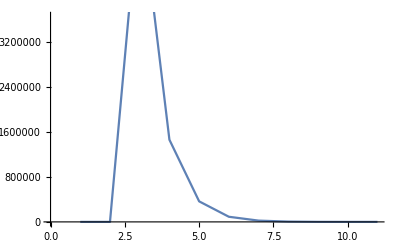

```mathematica
ListPlot[Norm /@ huh[[1]],Joined->True]
```

```mathematica
lucaBasis=GenerateBasis[stateVar,polyRange//.lucaSubs,initPower,theShock,theMean//.lucaSubs,{sigma$u}//.lucaSubs,integOrder//.lucaSubs,shockPower,nonStateVar];
```

## check initialization

```mathematica
$ContextPath
```

{ProjectionInterface`,JLink`,TemplatingLoader`,PacletManager`,System`,Global`}

```mathematica
InstallJava[]
```

LinkObject[…]

```mathematica
$ContextPath
```

{ProjectionInterface`,JLink`,TemplatingLoader`,PacletManager`,System`,Global`}

```mathematica
Needs["ProjectionInterface`"]
```

```mathematica
ReinstallJava[]
```

LinkObject[…]

```mathematica
duh=LinkObject[…]
```

LinkObject["C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\Java\Windows-x86-64\bin\javaw" -classpath "C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\lib\JLink.jar" -Dcom.wolfram.jlink.libdir="C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\os\win64" -Xmx256m  -Djava.system.class.loader=com.wolfram.jlink.JLinkSystemClassLoader com.wolfram.jlink.Install -init "C:\Users\m1gsa00\AppData\Local\Temp\m-3d3ffcbf-b63e-4bb7-97bb-12c7d6aa40b7",147,7]

```mathematica
LinkConnectedQ[duh]
```

LinkObject::linkn: Argument LinkObject["\"C:\\Program Files\\Wolfram Research\\Mathematica\\10.0\\SystemFiles\\Java\\Windows-x86-64\\bin\\javaw\" -classpath \"C:\\Program Files\\Wolfram Research\\Math" … ".wolfram.jlink.JLinkSystemClassLoader com.wolfram.jlink.Install -init \"C:\\Users\\m1gsa00\\AppData\\Local\\Temp\\m-3d3ffcbf-b63e-4bb7-97bb-12c7d6aa40b7\"", 147, 7] in LinkConnectedQ[LinkObject["\"C:\\Program Files\\Wolfram Research\\Mathematica\\10.0\\SystemFiles\\Java\\Windows-x86-64\\bin\\javaw\" -classpath \"C:\\Program Files\\Wolfram Resea" … ".jlink.JLinkSystemClassLoader com.wolfram.jlink.Install -init \"C:\\Users\\m1gsa00\\AppData\\Local\\Temp\\m-3d3ffcbf-b63e-4bb7-97bb-12c7d6aa40b7\"", 147, 7]] has an invalid LinkObject number; the link may be closed.

LinkConnectedQ[LinkObject["C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\Java\Windows-x86-64\bin\javaw" -classpath "C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\lib\JLink.jar" -Dcom.wolfram.jlink.libdir="C:\Program Files\Wolfram Research\Mathematica\10.0\SystemFiles\os\win64" -Xmx256m  -Djava.system.class.loader=com.wolfram.jlink.JLinkSystemClassLoader com.wolfram.jlink.Install -init "C:\Users\m1gsa00\AppData\Local\Temp\m-3d3ffcbf-b63e-4bb7-97bb-12c7d6aa40b7",147,7]]

```mathematica
?*Link*
```

```mathematica
urlClass=LoadJavaClass["java.net.URL"]
```

JavaClass[java.net.URL,<>]

## Initialization

```mathematica
If[$OperatingSystem==="Windows",SetDirectory["g:/git/ProjectionMethodTools/ProjectionMethodToolsJava/code"]];
```

```mathematica
Get["prepPackages.mth"]
```

```mathematica
modelDiags[modEqns,tryMat,lucaBasis]
```

modelDiags[«JavaObject[lucaMod]»,{{0,0,0,0.292289,0,0,0,0},{0,0,0,0.5,0,0,0,0},{0,0,0,0.299289,0,0,0,0}},JLink`Objects`vm2`JavaObject9714448113598465]

```mathematica
Needs["JLink`"];InstallJava[];Needs["ProjectionInterface`"]
```

```mathematica
$ContextPath
```

{ProjectionInterface`,JLink`,TemplatingLoader`,PacletManager`,System`,Global`}